# Appendix Chapter. Semiintegration and fractional calculus

In this notebook you are asked to load data from the SERM/Data folder. To prepare for this copy the line below to an input cell, replace the file path with the file path for the “Data” folder on your computer and press ⌤
AppendTo[$Path,”(* path to *)/SERM/Data/”];
or
AppendTo[$Path,ToFileName[ {NotebookDirectory[],”Data”}]];

Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[EvaluationNotebook[],
PrintingStartingPageNumber->284,

PageHeaders->{
{Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12],Cell[TextData[{"Appendix 2"}], FontFamily->"Arial",FontSize->12],None},
{None,Cell[TextData[CounterBox["Section",CounterFunction:>(Part[{"Semiintegration","Fractional Calculus","Further reading"},#]&)]],FontFamily->"Arial",FontSize->12],Cell[TextData[{CounterBox["Page"]}], FontFamily->"Arial",FontSize->12]}},

PageFooters->{{None,None,None},{None,None,None}},
PrintingOptions-> {
"PrintingMargins"->{{90,90},{60,90}},
"PaperSize"->{596,794},
"PageSize"->{596,794},
"PageHeaderMargins"->{60,60},
"PageFooterMargins"->{30,30},
"FirstPageFace"->Right,
"FirstPageHeader"->False,
"FirstPageFooter"->False,
"PrintRegistrationMarks"-> False}];
```

```mathematica
ClearAll[𝒻,𝔽,ℝ,𝕋,𝒟,α];
𝔽=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","FaradayConstant"],"Value"];(*Faradays constant*)
ℝ=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","MolarGasConstant"],"Value"];(*gas constant*)
𝕋=298.;(*temperature*)

𝒻=𝔽/(ℝ*𝕋);
𝒟=1.*10^-5;(*diffusion coefficient of substrate in cm^2 s^-1*)
α=0.5; (*transfer coefficient*)
```

```mathematica
SetOptions[ListPlot,
Axes->False,
Frame->True,
GridLines->None,
ImageSize->288,
Joined->True];

SetOptions[ListLinePlot,
Axes->False,
Frame->True,
GridLines->None,
ImageSize->288];
```

```mathematica
opts2={ 
FrameLabel->{
Style["E-E°",FontFamily-> "Times New Roman",10,Black,Italic],
None,
None,
Style["√πχ",FontFamily-> "Times New Roman",10, Plain,Black]}, 
Joined -> True,
PlotStyle-> {Red,Blue},
Epilog-> {Arrow[{{0.04,-0.5},{.09,-0.5}}]
}
};
```

```mathematica
opts3={
FrameLabel->{
Style["E-E°",FontFamily-> "Times New Roman",10,Black,Italic],
None,
None,
Style["√πχ",FontFamily-> "Times New Roman",10,Plain,Black]}, 
Joined -> True,
PlotStyle-> {Red,Blue},
Epilog-> {
Arrow[{{0.04,-0.75},{.09,-0.75}}]
}
};
```

```mathematica
optionA={
AspectRatio-> 2,
ImageSize->{144,288} ,
Frame-> False, 
Axes-> False,
Joined-> True,
PlotStyle-> {Black,AbsoluteThickness[0.5]}
};
```

```mathematica
optionB={
AspectRatio-> 1/GoldenRatio,
ImageSize->288 ,
Frame-> False,
Axes-> False,
Joined-> True,
PlotStyle-> {Red,AbsoluteThickness[0.5]},
PlotRange->{Automatic,{-.07,.48}}
};
```

```mathematica
PrependTo[$Path,{
Union[DirectoryName /@ FileNames["*.dat",FileNameJoin[{NotebookDirectory[],"Data","*"}] ,2]],
Union[DirectoryName /@ FileNames["*.nb",FileNameJoin[{NotebookDirectory[],"Extra Notebooks","*"}] ,2]]
}];

$Path=Union[Flatten@$Path];
```

```mathematica
$Line=0;
```

AChapter.Section Semiintegration

The relationship between the current from steady state, semi-infinite diffusion reactions is shown in Fig AChapter.FigureCaption.

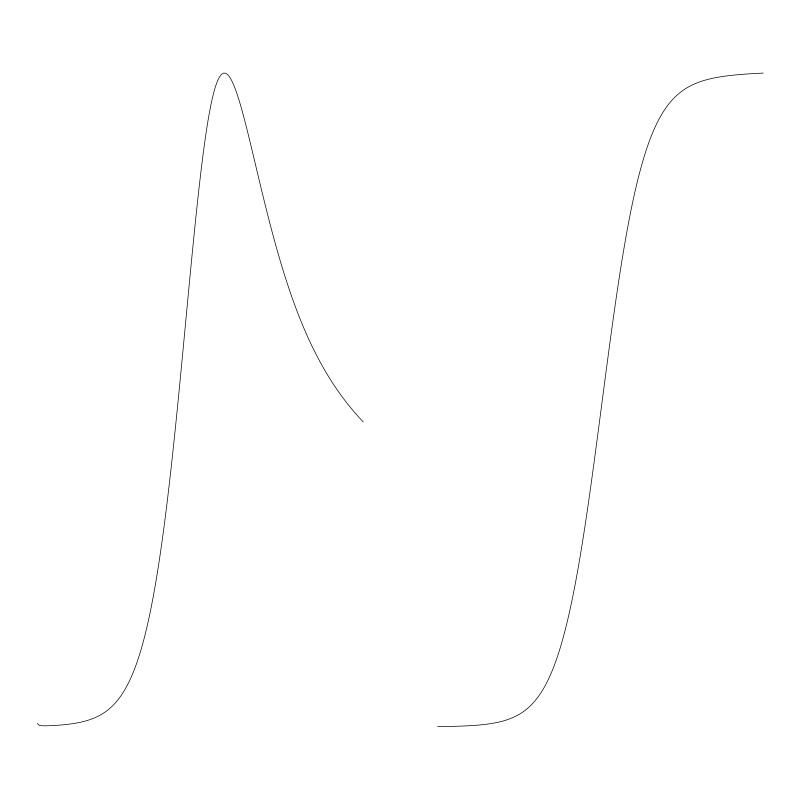

```mathematica
(* Import the file semiIntData.dat. *)
ClearAll[data,plot1,newData2,plot2,label];

data=Flatten[Import["semiIntData.dat"]];

semiIntS2[list_List]:=Module[{y1,y2,y3},
y1=Table[1/√(Length[list]-i+0.5), {i, Length[list],2,-1}];
y2=ListCorrelate[{1,1},list];
y3=(0.5/√Pi)*ListConvolve[y1,y2,{1,1},0]];


data=Flatten[data];
plot1=ListPlot[-data,optionA];
newData2=semiIntS2[data];
plot2=ListPlot[-newData2,optionA];

label=DisplayForm[FormBox[FractionBox[SuperscriptBox[StyleBox["d",FontFamily->"Times",FontSlant->"Plain"],RowBox[{"-1","/","2"}]],RowBox[{StyleBox["d",FontFamily->"Times",FontSlant->"Plain"],"",SuperscriptBox[RowBox[{StyleBox["t",FontFamily->"Times",FontSlant->"Italic"]}],RowBox[{"-1","/","2"}]]}]],TraditionalForm]];

Show[Graphics[{Rectangle[{0,0},{.5,1},plot1],Rectangle[{0.5,0},{1,1},plot2],Arrowheads[0.05],Arrow[{{0.4,0.5},{.6,.5}}],Text[label,{0.5,0.6},FormatType-> TraditionalForm]}],AspectRatio->1/GoldenRatio]

SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell]
```

Fig. AChapter.FigureCaption  The semi-integral of a linear sweep voltammogram produces a sigmoidal shaped plot.

The semi-integral of a linear sweep voltammogram transforms it to the sigmoidal shape normally associated with steady state reactions. Similarly the semi-derivative of a linear sweep voltammogram transforms it to a Gaussian peak shape normally associated with voltammograms of surface bound molecules. The semi-integral, I(t), of the current i(t) is given by

I(t)=1/π^(1/2)∫_0^t (i(τ))/(t-τ)^(1/2)ⅆτ

By dividing up the current into discrete time steps of width Δt as shown in Fig. A2.FigureCaption the semi-integral of the current i(t) becomes

I(kΔt)=1/π^(1/2)∑_(j=1)^k (i(jΔt-1/2 Δt)Δt^(1/2))/(k-j+1/2)^(1/2)

Code for Fig AChapter.FigureCaption

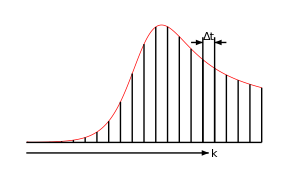

```mathematica
m1=Table[{{i,0},{i,-data⟦i⟧}},{i,20,Length[data],20}];
m2=Table[{i,-data⟦i⟧},{i,1,Length[data]}];

plot3=ListPlot[m2,optionB,
Epilog-> {
Line/@m1,Line[{{0,0},{400,0}}],
Line[{{300,0},{300,0.4}}],
Line[{{320,0},{320,0.4}}],
Text["Δt",{310,0.4}], 
Arrow[{{340,0.38},{320,.38}}],
Arrow[{{280,0.38},{300,.38}}],
Arrow[{{0,-0.04},{310,-0.04}}],
Text[Style["k",Italic],{320,-0.045}]}]

SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell]
```

Fig. AChapter.FigureCaption  Dividing the voltammogram into discrete sections of width Δ t.

In dimensionless form this becomes

X(kΔτ)=1/π^(1/2)∑_(j=1)^k (χ(jΔτ-1/2 Δτ)Δτ^(1/2))/(k-j+1/2)^(1/2)

where Δτ=(n F/R T)Δ E. Writing a procedural method to solve eqn (AChapter.AppendixEquation) in Mathematica is relatively straightforward:

```mathematica
ClearAll[semiIntD];

semiIntD[list_List,Δτ_]:=Table[{list⟦k,1⟧,(0.5*√(Abs[Δτ]/π))*∑_(i=2)^k ((list ⟦ i-1,2⟧+list⟦i,2⟧)/√(k-i+0.5))}, {k, 2, Length[list]}];
```

Unfortunately the implementation becomes very slow for large data sets therefore a faster functional approach needs to be developed. Let’s begin by expanding eqn (AChapter.AppendixEquation) and examining the first few terms:

For k=2: (data⟦1,2⟧+data⟦2,2⟧)/(√(2-2+1/2))

For k=3: (data⟦2,2⟧+data⟦3,2⟧)/(√(3-3+1/2))+(data⟦1,2⟧+data⟦2,2⟧)/(√(3-2+1/2))

For k=4:(data⟦3,2⟧+data⟦4,2⟧)/(√(4-4+1/2))+(data⟦2,2⟧+data⟦3,2⟧)/(√(4-3+1/2))+(data⟦1,2⟧+data⟦2,2⟧)/(√(4-2+1/2))

Focussing on the numerator notice that it contains combinations of adjacent terms in the data list that have been added together eg. data⟦1,2⟧+data⟦2,2⟧, data⟦2,2⟧+data⟦3,2⟧, data⟦3,2⟧+data⟦4,2⟧, and so on. If a discrete semi-integration was applied to a list of data = {a, b, c, d, e} the numerator would therefore contain terms a + b, b + c, c + d, d + e. These combinations can be generated with ListCorrelate, for example:

```mathematica
shortList={a,b,c,d,e};
ListCorrelate[{x,y},shortList]
```

{a x+b y,b x+c y,c x+d y,d x+e y}

therefore

```mathematica
y2=ListCorrelate[{1,1},shortList]
```

{a+b,b+c,c+d,d+e}

Focusing now on the denominator, for each term the dominator is given by:

```mathematica
y1=Table[1/Sqrt[Length[shortList]-i+1/2],{i,Length[shortList],2,-1}]
```

{√2,√(2/3),√(2/5),√(2/7)}

In order to devise a functional method for the semi-integration the task becomes one of combining elements of the two lists y1 and y2. ListConvolve enables this to be done. Consider some examples of how ListConvolve operates.

```mathematica
ListConvolve[{x,y},shortList]
```

{b x+a y,c x+b y,d x+c y,e x+d y}

and

```mathematica
ListConvolve[{a,b,c},{u,v,w}]
```

{c u+b v+a w}

but

```mathematica
ListConvolve[{a,b,c},{u,v,w},{1,1}]
```

{a u+c v+b w,b u+a v+c w,c u+b v+a w}

and

```mathematica
ListConvolve[{a,b,c},{u,v,w},{1,1},1]
```

{b+c+a u,c+b u+a v,c u+b v+a w}

therefore

```mathematica
ListConvolve[{a,b,c},{u,v,w},{1,1},0]
```

{a u,b u+a v,c u+b v+a w}

Returning to our problem it follows that the semi-integration can be generated by

```mathematica
m1=ListConvolve[y1,y2,{1,1},0]
```

{√2 (a+b),√(2/3) (a+b)+√2 (b+c),√(2/5) (a+b)+√(2/3) (b+c)+√2 (c+d),√(2/7) (a+b)+√(2/5) (b+c)+√(2/3) (c+d)+√2 (d+e)}

The output above is the semi-integration of the list shortlist and contains one less element than the original data list. Normally one would want to do the convolution on a two column {potential, current} list of data and return a two column {potential, semi-integrated data} list. Sticking with this example we first must drop the final term from shortlist so that shortlist and m1 have the same length.

```mathematica
data1=Drop[shortList,-1]
```

{a,b,c,d}

The two lists, data1 and m1, can be combined by either

```mathematica
Table[{data1⟦i⟧,m1⟦i⟧},{i,Length[m1]}]//N
```

{{a,1.41421 (a+b)},{b,0.816497 (a+b)+1.41421 (b+c)},{c,0.632456 (a+b)+0.816497 (b+c)+1.41421 (c+d)},{d,0.534522 (a+b)+0.632456 (b+c)+0.816497 (c+d)+1.41421 (d+e)}}

or

```mathematica
MapThread[{#1,#2}&,{data1,m1}]//N
```

{{a,1.41421 (a+b)},{b,0.816497 (a+b)+1.41421 (b+c)},{c,0.632456 (a+b)+0.816497 (b+c)+1.41421 (c+d)},{d,0.534522 (a+b)+0.632456 (b+c)+0.816497 (c+d)+1.41421 (d+e)}}

All these steps can be combined to create a function that takes a {potential, current} list and returns a {potential, semi-integrated current} list. The functional method performs the calculation approximately 300 times faster than the procedural method.

```mathematica
ClearAll[semiIntD2];

semiIntD2[list_List,Δτ_]:=Module[{y1,y2,y3,col1,col2},
(* separate the two columns *)
col1=Drop[list⟦All,1⟧,-1];
col2=list⟦All,2⟧;

y1=Table[1/√(Length[col2]-i+0.5), {i, Length[col2],2,-1}];
y2=ListCorrelate[{1,1},col2];
y3=(0.5*√Abs[Δτ]/√Pi)*ListConvolve[y1,y2,{1,1},0]//N;MapThread[{#1,#2}&,{col1,y3}]]
```

Code for Fig AChapter.3

```mathematica
data2=Import["semiIntData2.dat"];
```

The data consists of voltammetric current in 1 mV steps:

```mathematica
Short[data2,7]
```

{{0.2,-0.00258816},{0.199,-0.00174115},{0.198,-0.00129241},{0.197,-0.00104832},{0.196,-0.000912407},{0.195,-0.000835677},{0.194,-0.000792673},«387»,{-0.194,-0.211091},{-0.195,-0.21048},{-0.196,-0.209875},{-0.197,-0.209275},{-0.198,-0.208681},{-0.199,-0.208092}}

```mathematica
semiInt=semiIntD2[data2,𝒻*.001];

ListLinePlot[{semiInt,data2},
MultiaxisArrangement->All,
PlotStyle->{Directive[Black,DotDashed],Directive[Black]},opts2]
```

-Graphics-

Fig. AChapter.FigureCaption  Plot of the linear sweep voltammogram containing 400 pairs of data points and its semi-integration.

## AChapter.Section Fractional Calculus

Semi-derivatives and semi-integrals can be considered as a special case of differo-integrals of fractional order. The relationship between a derivative and integral is shown eqn (AChapter.AppendixEquation) where the integration of f(y) is shown as equivalent to the inverse differentiation. Put another way negative orders of differentiation are equivalent to integration.

d^(-1)/dx^(-1)f≡∫_0^∞ f(y)ⅆy

The Rieman-Louiville definition of a fractional derivative is

d^q/(d(x-a))^q f=1/(Γ(-q))∫_0^∞ (x-y)^(-q-1)f(y)ⅆy	for q<0

so that a fractional derivative, i.e. positive q, can be written as

d^q/(d(x-a))^q f≡d^n/dx^n(d^(q-n)/(d(x-a))^(q-n)f)	for q-n<0

d^q/(d(x-a))^q f≡d^n/dx^n(1/(Γ(n-q))∫_0^∞ (x-y)^(-q+n-1)f(y)ⅆy)	for n<q

The Laplace transform of the Rieman-Louiville fractional derivative is given by eqns (AChapter.AppendixEquation).

ℒ{d^q/dx^q f}=s^q ℒ{f}-∑_(k=0)^(q-1) s^k d^(q-1-k)/dx^(q-1-k)f(0)

If we try to perform non-integer differentiation using Mathematica an error message appears:

```mathematica
D[x^3,{x,0.7}]
```

2.23594 x^2.3

To perform the fractional derivative of powers we can modify the definition of a derivative by first unprotecting the function D.

```mathematica
Unprotect[D];

D[x_^m_,{x_,q_}]:=Gamma[m+1]/Gamma[m-q+1] x^(m-q)/;Head[q]== Real || Head[q]== Rational||Head[q]== Complex

Protect[D];
```

```mathematica
D[x^3,{x,0.7}]
```

2.23594 x^2.3

and

```mathematica
D[x^3,{x,1/2}]
```

(16 x^(5/2))/(5 √π)

In light of eqn (AChapter.AppendixEquation) the fractional integral, α, of the current becomes

I(t)=1/(Γ(α))∫_0^t (i(τ))/(t-τ)^α ⅆτ

By dividing up the current into discrete time steps of width Δ t as shown in Fig. A2.FigureCaption the fractional integral of the current i(t) becomes

I(kΔt)=1/(Γ(α))∑_(j=1)^k (i(jΔt-1/2 Δt)Δt^(1-α))/(k-j+1/2)^α

In dimensionless form this becomes

X(kΔτ)=1/(Γ(α))∑_(j=1)^k (χ(jΔτ-1/2 Δτ)Δτ^(1-α))/(k-j+1/2)^α

Writing a functional method to solve eqn (AChapter.AppendixEquation) in Mathematica requires only small modifications to the semi-integration method.

```mathematica
ClearAll[fractIntB];

fractIntB[list_List,α_/;1.>α>0.,Δτ_]:=Module[{y1,y2,y3,col1,col2},

col1=Drop[list⟦All,1⟧,-1];
col2=list⟦All,2⟧;

y1=Table[(Length[col2]-i+0.5)^(-α), {i, Length[col2],2,-1}];
y2=ListCorrelate[{1,1},col2];

y3=(0.5*Abs[Δτ]^(1-α)/Gamma[α])*ListConvolve[y1,y2,{1,1},0]//N;MapThread[{#1,#2}&,{col1,y3}]]
```

```mathematica
fractInt=fractIntB[data2,.75,𝒻*.001];

ListLinePlot[{fractInt,data2},
MultiaxisArrangement->All,
PlotStyle->{Directive[Black,DotDashed],Directive[Black]},opts3]
```

-Graphics-

Fig. A2.FigureCaption  Plot of the linear sweep voltammogram and its fractional integral of order 0.75.

## Further reading

Bauman, G. (1999).  Mathematica in Education and Research, 8, 58-65. (This article can be downloaded from the WRI Information Center).